# Bell's Theorem: CHSH inequality

```mathematica
Column@EntityValue[Entity["Person","JohnStewartBell::364v4"],{"Image","BirthDate","DeathDate","NotableFacts"}]
```

-Graphics-
Thu 28 Jun 1928
Mon 1 Oct 1990
{Originated Bell's theorem in 1964, relating to hidden variable theories in quantum physics,Known for work in superdeterminism and formulation of the paradox known as Bell's spaceship paradox,Worked for most of his career at the European Organization for Nuclear Research (CERN),Nominated for the Nobel Prize in Physics in 1990, but died before the selection was made}

Bell's inequalities are examined within the Wolfram quantum framework, using the standard language of quantum computation. A straightforward computational approach is employed to comprehend the underlying derivations of those equations, fully derived from standard quantum computation.

## Entangled states, correlations, and measurement

Consider a 2-qubit quantum system that is prepared in the following quantum state

```mathematica
ψm=QuantumState["PsiMinus"]
```

1/(√2)01-1/(√2)10

Check if it is an entangled state:

```mathematica
QuantumEntangledQ[ψm]
```

True

which is, of course, maximally entangled:

```mathematica
QuantumEntanglementMonotone[ψm]
```

1

An entangled state is a state that cannot be written as product of two states ρ_1⊗ρ_2. This possibility can be tested using QuantumEntangledQ which returns as True or False.

Let’s define a unit vector in 3D (which is parametrized by two angles):

```mathematica
a[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
```

Given two unit vectors, let’s find the angle between:

```mathematica
vecAngle=FullSimplify[VectorAngle[a[θ1,ϕ1],a[θ2,ϕ2]],Assumptions->{θ1∈Reals,θ2∈Reals,ϕ1∈Reals,ϕ2∈Reals}]
```

ArcCos[Cos[θ1] Cos[θ2]+Cos[ϕ1-ϕ2] Sin[θ1] Sin[θ2]]

Now let us calculate the quantum expectation (i.e. the mean value) of a composite operator as follows: ψ^-(a⃗)_1.σ⃗⊗(a⃗)_2.σ⃗ψ^- with ψ^-=1/(√2)(01-10) and σ⃗ the Pauli vector.

Define a Pauli vector:

```mathematica
σ[θ_,ϕ_]:=QuantumOperator[a[θ,ϕ].Table[PauliMatrix[i],{i,3}]]
```

Calculate  ψ^-(a⃗)_1.σ⃗⊗(a⃗)_2.σ⃗ψ^-:

```mathematica
ψm["Dagger"][QuantumTensorProduct[σ[θ1,ϕ1],σ[θ2,ϕ2]][ψm]]
```

QuantumState[…]

Note that the result is a scalar, but as an object, we treat it as a quantum state object, with 0 number of qudits (look at the summary box of above result). The actual scalar number can be extracted like this:

```mathematica
Φ12=FullSimplify[%["Number"]]
```

-Cos[θ1] Cos[θ2]-Cos[ϕ1-ϕ2] Sin[θ1] Sin[θ2]

The expectation value is related to the vector angle as follows:

```mathematica
-Cos[vecAngle]==Φ12
```

True

In other words: ψ^-(a⃗)_1.σ⃗⊗(a⃗)_2.σ⃗ψ^-=-cos(Φ_12) 
Remember this result. We will use it later within Bell’s inequality. But before jumping to Bell’s inequality, let’s explore how above expectation value can be calculated or obtained experimentally using quantum circuits.

For simplicity, let’s consider the case where qubit-1 is measured in Pauli-X basis, and qubit-2 in another basis which obtained by rotating Pauli-X basis by π/8 around z-axis

Define new basis (Pauli-X which is rotated by π/8 around z-axis) and label it:

```mathematica
newBasis=QuantumBasis[N@QuantumOperator[{"RZ",π/8}][QuantumBasis["X"]],"Label"->"(FractionBox[π, 8])_xz"];
```

Note I added N, just to enforce numeric calculations, which are faster.

Measure in Pauli-X basis on qubit-1, in new basis on qubit-2, when the system is prepared in ψ^-:

```mathematica
meas=QuantumMeasurementOperator["X"]@QuantumMeasurementOperator[newBasis,{2}]@QuantumState["PsiMinus"];
```

Find the measurement probabilities:

```mathematica
prob=meas["Probabilities"]
```

<|𝓍_+0→0.0190301,𝓍_+1→0.48097,𝓍_−0→0.48097,𝓍_−1→0.0190301|>

Note the first and last results correspond to + eigenvalue (their multiplication) and middle ones -. So for the mean value, we do as follows:

```mathematica
prob[[1]]+prob[[4]]-(prob[[2]]+prob[[3]])
```

-0.92388

Taking cos^-1 of above result (note ψ^-(a⃗)_1.σ⃗⊗(a⃗)_2.σ⃗ψ^-=-cos(Φ_12)) one can confirm:

```mathematica
ArcCos[-%]==π/8
```

True

which is what we expected. Now let’s focus on the circuit version.

The following quantum circuit prepare a 2-qubit quantum system in ψ^- first, and then two measurements are performed on 2-qubits (as described previously).

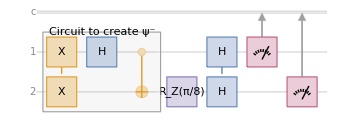

```mathematica
qc1=QuantumCircuitOperator[{QuantumCircuitOperator[{"X"->{1,2},"H","CNOT"},"Circuit to create ψ^-"],{"RZ",π/8}->2,"H"->{1,2},{1},{2}}];
qc1["Diagram"]
```

The above circuit is the one you see in many literature, mostly because that is how you send it to a Quantum Processing Unit (QPU, ie a quantum hardware). However, in our framework, you can define the measurement in any basis, for example:

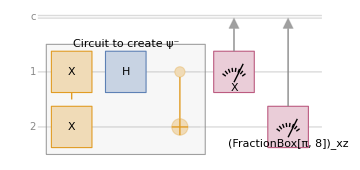

```mathematica
qc2=QuantumCircuitOperator[{QuantumCircuitOperator[{"X"->{1,2},"H","CNOT"},"Circuit to create ψ^-"],QuantumMeasurementOperator["X"],QuantumMeasurementOperator[newBasis,{2}]}];
qc2["Diagram"]
```

Note that those light purple boxes representing measurement are fundamentally different from other boxes representing usual gates. But that is a different story (refer to this for more details).

The above circuits are equivalent. However, for the sake of communicating with a QPU, some transpilers may have some issues with defining measurements for a customized basis. So let’s focus on first circuit:

```mathematica
qc1["Diagram"]
```

-Graphics-

In above circuit, (a⃗)_1->{θ=π/2,ϕ=0} (measurement on qubit-1) and (a⃗)_2->{θ=π/2,ϕ=π/8} (measurement on qubit-2). Note the Hadamard (H) boxes before measurements are transforming the measurement to Pauli-X, and R_z rotation rotates it by an angle in xy-plane. So the correlation function should be -cos(π/8)

Find the probabilities from above circuit:

```mathematica
prob1=FullSimplify/@qc1[]["Probabilities"]
```

<|00→1/2 Sin[π/16]^2,01→1/4 (1+Cos[π/8]),10→1/4 (1+Cos[π/8]),11→1/2 Sin[π/16]^2|>

Calculate the correlation function:

```mathematica
prob1[00]+prob1[11]-(prob1[01]+prob1[10])//FullSimplify
```

-Cos[π/8]

which is, of course, what we expected.

Note that the experimental results that one gets out of a QPU is counters per measurement results; something like this:

```mathematica
exp=qc1[]
```

QuantumMeasurement[…]

Simulate measurement results for 1024 shots:

```mathematica
counts=Counts[exp["SimulatedMeasurement",1024]]
```

<|10→498,01→484,11→23,00→19|>

Calculate the corresponding correlation (using frequency of occurrence for each result):

```mathematica
(counts[00]+counts[11]-(counts[01]+counts[10]))/1024//N
```

-0.917969

which is what we expected (close enough, given number of shots)

```mathematica
-Cos[π/8]//N
```

-0.92388

Now let’s see how those correlations are used in Bell inequality

## Bell’s inequality

There are many good literature on the Bell’s inequality and what it implies. If you are looking for a short paper, with some nice [personal] history, we highly recommend this preprint by GianCarlo Ghirardi: John Stuart Bell: recollections of a great scientist and a great man.

Let us rephrase the reasoning behind the derivation of Bell’s inequality (following Ghirardi):

“Experimental Perfect Correlations” ∧ “Bell’s Locality” ⇒ “Determinism”
	“Determinism” ∧ “Bell’s Locality” ⇒ “Bell’s Inequality”
	“General Quantum Correlations” ⇒ ¬ “Bell’s Inequality”
	¬“Bell’s  Inequality” ⇒ ¬ “Determinism” ∨ ¬“Bell’s Locality”
	Summarizing: “Natural Processes” ⇒ ¬“Bell’s Locality”, i.e.: Nature is non-locally causal.

From locality to determinism. If distant measurements on the singlet state always give opposite results (perfect correlations), and if we insist that what happens at one site cannot depend on what happens at the other (Bell's Locality), then the outcomes must have been fixed in advance, determinism follows as a consequence.
If outcomes are predetermined and Bell's Locality holds, then the correlations between measurement results are constrained, they must satisfy Bell's inequality.
Quantum mechanics violates the inequality. The correlations predicted by quantum theory (and confirmed by experiment) exceed the bound imposed by Bell's inequality.
Something must give. Since the inequality is violated, at least one of its premises fails: either determinism is wrong, or Bell's Locality is wrong (or both).
Locality fails regardless. Suppose we try to save things by abandoning determinism. But then we lose the only local explanation for why perfect correlations occur. Without locality, we can't derive determinism, and without determinism, we can't locally account for the perfect correlations we actually observe. So dropping determinism alone doesn't help; locality must fail too.

Well, if anything, let's comment on Bell’s Locality, which implies that measurement probabilities 	(accessible or not, to observer) at two space-like regions are independent.

Bell’s inequality in the CHSH form can be written as follows: |E_μ((a⃗)_1,(a⃗)_2)-E_μ((a⃗)_1,(a⃗)_4)+E_μ((a⃗)_3,(a⃗)_2)+E_μ((a⃗)_3,(a⃗)_4)|<=|E_μ((a⃗)_1,(a⃗)_2)-E_μ((a⃗)_1,(a⃗)_4)|+|E_μ((a⃗)_3,(a⃗)_2)+E_μ((a⃗)_3,(a⃗)_4)|<=2
with μ the accessible variable of the system that specifies the quantum state (eg the preparation step). Note there is another variable in the derivation of Bell’s inequality, usually denoted b λ, which is inaccessible variable specifying the quantum state (the quantum world/level is obtained by averaging over λ).

Also, E_μ((a⃗)_i,(a⃗)_j) is identified as the quantum expectation value. Assuming that the state is ψ^- and using the result for the correlation function (ψ^-(a⃗)_1.σ⃗⊗(a⃗)_2.σ⃗ψ^-=-cos(Φ_12) with Φ_12 the vector angle between (a⃗)_1 and (a⃗)_2), the left-side of above inequality can be written as:

```mathematica
Abs[Cos[VectorAngle[a1,a2]]-Cos[VectorAngle[a1,a4]]]+Abs[Cos[VectorAngle[a3,a2]]+Cos[VectorAngle[a3,a4]]]≤ 2
```

For example, let us consider this case: VectorAngle[a1,a2]=VectorAngle[a3,a2]=VectorAngle[a3,a4]=ϕ and VectorAngle[a1,a4]=3ϕ. 
Plugging this into above equation, and one can plot regions of ϕ such that the Bell’s inequality is violated:

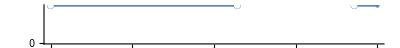

```mathematica
NumberLinePlot[Not[Abs[Cos[ϕ]-Cos[3ϕ]]+Abs[2Cos[ϕ]]≤2],{ϕ,0,2π/3},Ticks->{{0,π/6,π/3,π/2,2π/3}},PlotLabel->"Regions within the Bell's inequality are violated"]
```

One can obtain those regions (where the Bell’s inequality is violated) explicitly:

```mathematica
Reduce[Abs[Cos[ϕ]-Cos[3ϕ]]+Abs[2Cos[ϕ]]>2&&0≤ϕ≤2π/3,ϕ]
```

0<ϕ<2 ArcTan[√(-3+2 √3)]||2 ArcTan[√(1/3 (3+2 √3))]<ϕ≤(2 π)/3

One can also find the maximum violation, which happens at π/4:

```mathematica
NMaximize[Abs[Cos[ϕ]-Cos[3ϕ]]+Abs[2Cos[ϕ]],ϕ]
```

{2.82843,{ϕ→0.785398}}

## Explore Bell’s inequality in a quantum circuit

Given four unit vectors (a⃗)_i, we will focus on this case: VectorAngle[a1,a2]=VectorAngle[a3,a2]=VectorAngle[a3,a4]=ϕ and VectorAngle[a1,a4]=3ϕ. 
To find those four correlation functions, we will design four circuit as follows:

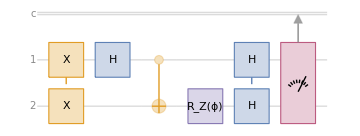

```mathematica
corQC12=QuantumCircuitOperator[{"X"->{1,2},"H","CNOT",{"RZ",ϕ}->2,"H"->{1,2},{1,2}}];
corQC12["Diagram"]
```

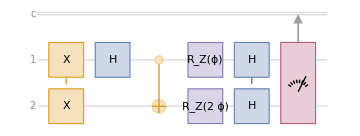

```mathematica
corQC32=QuantumCircuitOperator[{"X"->{1,2},"H","CNOT",{"RZ",ϕ},{"RZ",2ϕ}->2,"H"->{1,2},{1,2}}];
corQC32["Diagram"]
```

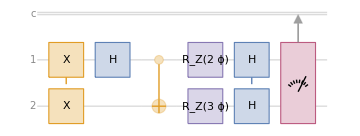

```mathematica
corQC34=QuantumCircuitOperator[{"X"->{1,2},"H","CNOT",{"RZ",2ϕ}->1,{"RZ",3ϕ}->2,"H"->{1,2},{1,2}}];
corQC34["Diagram"]
```

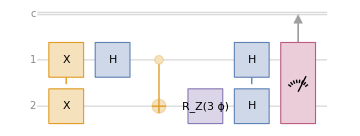

```mathematica
corQC14=QuantumCircuitOperator[{"X"->{1,2},"H","CNOT",{"RZ",3ϕ}->2,"H"->{1,2},{1,2}}];
corQC14["Diagram"]
```

Now let’s calculate the corresponding correlations, using above circuits. We will find those correlations analytically, using our quantum framework.
Of course, one can find the numerical value of those correlations (theoretically, by some simulation as shown in the previous section, or experimentally using some QPUs).

```mathematica
$Assumptions=0≤ϕ≤2π/3;
```

Measurement probabilities from circuit to find E_μ((a⃗)_1,(a⃗)_2):

```mathematica
meas12=FullSimplify/@corQC12[]["Probabilities"]
```

<|00→1/4 (1-Cos[ϕ]),01→1/4 (1+Cos[ϕ]),10→1/4 (1+Cos[ϕ]),11→1/4 (1-Cos[ϕ])|>

```mathematica
cor12=FullSimplify[(#[00]+#[11]-#[01]-#[10])&@meas12]
```

-Cos[ϕ]

Measurement probabilities from circuit to find E_μ((a⃗)_3,(a⃗)_2):

```mathematica
meas32=FullSimplify/@corQC32[]["Probabilities"]
```

<|00→1/4 (1-Cos[ϕ]),01→1/4 (1+Cos[ϕ]),10→1/4 (1+Cos[ϕ]),11→1/4 (1-Cos[ϕ])|>

```mathematica
cor32=FullSimplify[(#[00]+#[11]-#[01]-#[10])&@meas32]
```

-Cos[ϕ]

Measurement probabilities from circuit to find E_μ((a⃗)_3,(a⃗)_4):

```mathematica
meas34=FullSimplify/@corQC34[]["Probabilities"]
```

<|00→1/4 (1-Cos[ϕ]),01→1/4 (1+Cos[ϕ]),10→1/4 (1+Cos[ϕ]),11→1/4 (1-Cos[ϕ])|>

```mathematica
cor34=FullSimplify[(#[00]+#[11]-#[01]-#[10])&@meas34]
```

-Cos[ϕ]

Measurement probabilities from circuit to find E_μ((a⃗)_1,(a⃗)_4):

```mathematica
meas14=FullSimplify/@corQC14[]["Probabilities"]
```

<|00→1/2 Sin[(3 ϕ)/2]^2,01→1/4 (1+Cos[3 ϕ]),10→1/4 (1+Cos[3 ϕ]),11→1/2 Sin[(3 ϕ)/2]^2|>

```mathematica
cor14=FullSimplify[(#[00]+#[11]-#[01]-#[10])&@meas14]
```

-Cos[3 ϕ]

Plug them into Bell’s inequality:

```mathematica
Abs[cor12-cor14]+Abs[cor32+cor34]≤2
```

Plot the region that Bell’s inequality (above) is violated:

```mathematica
NumberLinePlot[Not[Abs[cor12-cor14]+Abs[cor32+cor34]<=2],{ϕ,0,2π/3},Ticks->{{0,π/6,π/3,π/2,2π/3}},PlotLabel->"Regions within the Bell's inequality is voilated"]
```

-Graphics-

Certainly, the aforementioned circuits may be executed using existing QPUs to obtain empirical correlations. However, such findings hold little value unless we know the details of experimental setting employed, to address problems commonly known as “loopholes” (such as the locality loophole).

## Reference

GianCarlo Ghirardi: John Stuart Bell: recollections of a great scientist and a great man, arXiv:1411.1425v1 (2014).

John S. Bell: The Trieste lecture of John Stewart Bell, Journal of Physics A: Mathematical and Theoretical 40, 2919–2933 (2007).

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFrameworkLoader`

Wolfram/QuantumFramework/tutorial/Bellstheorem

### Keywords